```mathematica
∶h
```

# Pet Bottle Rocket

```mathematica
ClearAll["Global`*"]
```

## Initialization cells:

## Physical constants:

```mathematica
atmpressure = 1.01*10^5; (* Atmosferic pressure in Pa *)
gamma = 7/5; (* Adimensional ratio of specific heats *)
gravityacc = 9.8; (* gravity in m/s^2 *)
waterdensity = 997 ; (* water density in kg/m^3 *)
airdensity = 1.225; (* air density kg/m^3 *)
temperature=273+20;
gasconstant=8.314 /0.028;

repphysicsconstats = {
Patm->atmpressure,  
γ->gamma, 
g->gravityacc, 
RhoWater->waterdensity,
RhoAir->airdensity,
T0->temperature,
Rm->gasconstant
};
```

## Initial conditions:

```mathematica
dragcoeficient=0.5; (* Rocket drag coeficient *)
initialpressure = 7 10^5; (* Initial rocket bottle pressure in Pa *)

volumelaunchtube = 0.0005; (* Volume of the launch tube chamber in m^3 *)
volumebottle  =2.1 /1000; (* Volume of the bottle in m^3*)
volumewater0 =0.5 / 1000; (* Initial volume of water in m^3 *)

drymass = 0.1; (* Dry bottle mass in kg *)

launchtubesize = 0.15;(* Launch tube size in m *)
xseclaunchtubext = 0.0045^2 π; (* External crossectional area of the launch tube in m^2 *) 
xseclaunchtubint = 0.0045^2 π; (* Internal crossectional area of the launch tube in m^2 *)

bottleradius1 = 0.0525; (* Radius of the bottle at the start of nozzle in m *)
bottleradius2 = 0.0022; (* Radius of the bottle at the end of the nozzle in m *)
bottleheight = 0.27; (* Bottle height in m *)
nozzlesizeA = 0.075; (* Size of the nozzle in m *)
nozzlesizeB=0.015;
secarea=π*bottleradius1^2;
```

```mathematica
initialconditions = {
Dc->dragcoeficient,
P0->initialpressure,
Vl->volumelaunchtube,
Vb->volumebottle, 
Vw0->volumewater0, 
Mb->drymass,
M0->drymass + volumewater0*waterdensity, 
Lt->launchtubesize, 
Ato->xseclaunchtubext, 
Ati->xseclaunchtubint, 
r1->bottleradius1,
r2->bottleradius2, 
Hb->bottleheight, 
NsA->nozzlesizeA,
NsB->nozzlesizeB,
Ab->secarea,
As->π*bottleradius2^2
};
```

## Others:

```mathematica
analysistime=1; (* Maximum time of evaluation for solving the differential equations in s *)
```

## Defining the bottle:

```mathematica
radius[y_]:= Piecewise[{{r2, 0<=y<NsB},{r2+(r1-r2)*((y-NsB)/(NsA-NsB)), NsB<=y<NsA}, {r1,NsA<y<=Hb}}]/.initialconditions; (* Returns the radius of the bottle given a Y coordinate *)
xsec[y_]:=π*radius[y]^2 (* Returns the crossectional area of the bottle given a Y coordinate *)
watervolume[h_]:= Integrate[xsec[z],{z,0,h}, Assumptions->{h>=0, h∈Reals}]; (* Water volume in the bottle given the water level *)
```

## Visualizing the bottle:

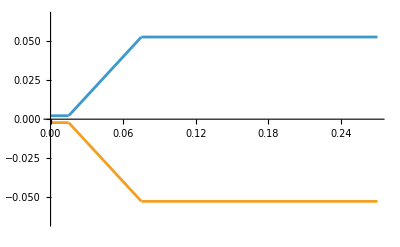

```mathematica
ContourRange := {{0, bottleheight}, {-r1*5/4, r1*5/4}} /.initialconditions (* Defines the plot range *)
Plot[{radius[x], -radius[x]}, {x, 0, bottleheight}, PlotRange->ContourRange](* Plot the shape of the bottle *)
```

Finding the initial water level:

```mathematica
waterlevel0=h/.FindRoot[(watervolume[h]- Vw0)/.initialconditions,{h,0}] (* Initial water level *)
```

0.111844

## Dynamics:

```mathematica
dragforce[t_]:=-1/2(Dc *RhoAir *Ab *y'[t]* Abs[y'[t]]) /.repphysicsconstats/.initialconditions(* Air resistance force *)
```

## Launch phase:

### Defining functions:

```mathematica
vinit := Vl+Vb-Vw0-Lt*(Ato-Ati) (* Initial volume of air *)
rrho[t_] := (vinit / (vinit + y[t] * Ato)) (* Air density ratio in function of time *)
pressure[t_] := P0 * (rrho[t])^γ  (* Pressure at bottle in function of time *)
```

### Defining the thrust force:

```mathematica
fthrlaunchphase[t_] := (pressure[t] - Patm) * Ato (* Thurst force *)
```

### Defining the differential equation and solving it:

```mathematica
diffeqy1=y''[t]==(fthrlaunchphase[t]+dragforce[t])/M0-g /. initialconditions /.repphysicsconstats; (* Position differential equation *)
```

```mathematica
ylaunchphase=(y/.NDSolve[{diffeqy1, y'[0]==0, y[0]==0}, y,{t, 0, analysistime}]//Flatten)[[1]]; (* Numerically solves the differential equation *)
```

```mathematica
velylaunchphase=ylaunchphase'; (* Velocity of the rocket at any instant *)
```

```mathematica
maxtimelaunchphase=t/.FindRoot[ylaunchphase[t]-Lt/.initialconditions, {t, 0,analysistime}]; (* Instant when this phase ends *)
```

### Plotting the height:

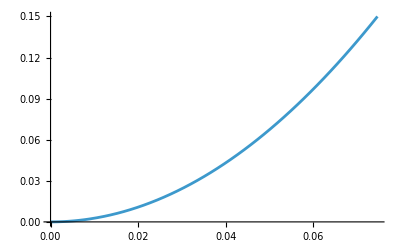

```mathematica
Plot[ylaunchphase[t], {t, 0, maxtimelaunchphase}]
```

```mathematica
P1=pressure[t]/.{y[t]->ylaunchphase[t]}/.repphysicsconstats/.initialconditions/.{t->maxtimelaunchphase}; 
T1=T0*(rrho[t])^(γ-1)/.{y->ylaunchphase}/.{t->maxtimelaunchphase}/.repphysicsconstats/.initialconditions;
```

## Water phase:

### Defining auxiliary functions:

```mathematica
B1[h_]:=Integrate[xsec[0]/xsec[z], {z, 0, h}, Assumptions->(h∈Reals)]
B2[h_]:=1/2 * ((xsec[0] / xsec[h])^2 - 1)
B3[h_]:=((Vb - Vw0) / (Vb - watervolume[h]))^γ
```

```mathematica
mtot[t_]:=Mb+RhoAir*(Vb-Vw0)+RhoWater*watervolume[h[t]] (* Total mass in function of time *)
```

### Defining the thrust and internal forces:

```mathematica
fthrwaterphase[t_]:=waterdensity*xsec[0]*uout[t]^2 (* Thrust force *)
fintwaterphase[t_]:=-RhoWater*xsec[0]*(h[t]*uout'[t]+(xsec[0]/xsec[h[t]])*uout[t]^2) (* Internal force*)
```

### Defining the differential equations and solving them:

```mathematica
(* For this section, we are solving the system of differential equations for: uout[t] -> Fluid escape velocity, h[t] -> fluid height, y[t] -> y-coordinate of the rocket. *)
```

```mathematica
diffequout=B1[h[t]]*uout'[t]+B2[h[t]]*uout[t]^2+B3[h[t]]*P1/RhoWater-Patm/RhoWater+(y''[t]+g)*h[t]==0 /. repphysicsconstats /.initialconditions; (* uout[t] differential equation *)
diffeqh=h'[t]==xsec[0]*uout[t] / xsec[h[t]] /.repphysicsconstats/.initialconditions; (* h[t] differential equation *)
diffeqy2=y''[t]==(fthrwaterphase[t] + fintwaterphase[t]+dragforce[t])/ mtot[t] - g /.repphysicsconstats/.initialconditions; (* y[t] differential equation *)
```

```mathematica
edosol=NDSolve[{diffequout, diffeqh, diffeqy2, uout[0]==0,h[0]==waterlevel0,y[0]==ylaunchphase[maxtimelaunchphase], y'[0]==velylaunchphase[maxtimelaunchphase],WhenEvent[h[t]<=0.0,"StopIntegration"]}, {y, uout, h}, {t, 0, analysistime}
]//Flatten; (* Numerically solves the differential equations *)
```

```mathematica
ywaterphase=y/.edosol;
waterheight=h/.edosol;
watervelocity=uout/.edosol;
totalmass[t_]=mtot[t]/.{h->ywaterphase}/.initialconditions/.repphysicsconstats;
```

```mathematica
maxtimewaterphase=t/.FindRoot[waterheight[t], {t, 0.01}]
```

InterpolatingFunction::dmval: Input value {1.84406} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.92774} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99631} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

1.13127

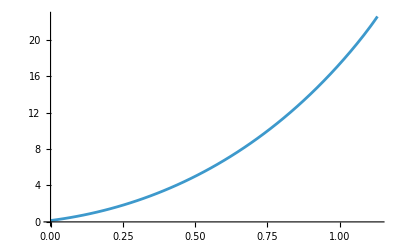

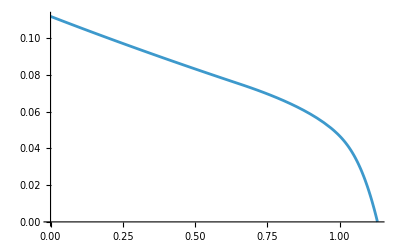

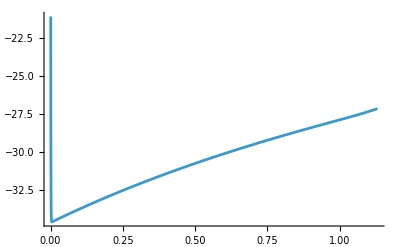

```mathematica
Plot[ywaterphase[t],{t,0, maxtimewaterphase}]
Plot[waterheight[t], {t, 0,maxtimewaterphase}]
Plot[watervelocity[t], {t, 0,  maxtimewaterphase}]
```

```mathematica
P2=P1*((Vb-Vw0)/Vb)^γ /.initialconditions/.repphysicsconstats
T2=T1*((Vb-Vw0)/Vb)^(1-γ)/.initialconditions/.repphysicsconstats
```

475338.

326.077

## Gas phase:

```mathematica
Mtot1[t_]:=Mb+rhot[t]*Vb/.initialconditions/.repphysicsconstats;
Rho2=RhoAir*(Vb-Vw0)/(Vb-watervolume[H[t]])/. {H->waterheight}/.{t->maxtimewaterphase}/.initialconditions/.repphysicsconstats;
tau=Vb / (As * Sqrt[γ*Rm*T2])*(2/(γ-1))*((γ+1)/2)^((γ+1)/(2(γ-1)));
Pt[t_]:=P2*(1+t/tau)^((2γ)/(1-γ));
fthrgasphase[t_]:=2 Pt[t] As (2 / (γ + 1))^(1/(γ-1))-Patm As/.initialconditions/.repphysicsconstats;
rhot[t_]:=(Pt[t]/P2)^(1/γ)*Rho2;
diffeqy3=y''[t]==(fthrgasphase[t]+dragforce[t])/Mtot1[t]-g/.initialconditions/.repphysicsconstats;
```

InterpolatingFunction::dmval: Input value {1.13127} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
edosol1=NDSolve[{diffeqy3, y[0]==ywaterphase[maxtimewaterphase], y'[0]==ywaterphase'[maxtimewaterphase]},y,{t,0,analysistime}];
ygasphase=y/.Flatten[edosol1];
```

InterpolatingFunction::dmval: Input value {1.13127} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
maxtimegasphase=t/.FindRoot[Pt[t]-Patm/.initialconditions/.repphysicsconstats,{t,0}];
```

## No thrust phase:

```mathematica
diffeqy4=y''[t]==-g+dragforce[t]/m;
```

```mathematica
(*yfinal=NDSolveValue[{diffeqy4, y[0]==ywaterphase[maxtimewaterphase], y'[0]==ywaterphase'[maxtimewaterphase]}/.repphysicsconstats/.initialconditions/.m->(totalmass[maxtimewaterphase]), y, {t, 0, 100}];*)
```

```mathematica
yfinal=NDSolveValue[{diffeqy4, y[0]==ygasphase[maxtimegasphase], y'[0]==ygasphase'[maxtimegasphase]}/.repphysicsconstats/.initialconditions/.m->(Mtot1[maxtimegasphase]), y, {t, 0, 100}];
```

```mathematica
(*yfinal=NDSolveValue[{diffeqy3, y[0]==ylaunchphase[maxtimelaunchphase], y'[0]==ylaunchphase'[maxtimelaunchphase]}/.repphysicsconstats/.initialconditions/.m->(totalmass[0]), y, {t, 0, 100}];*)
```

## All phases:

```mathematica
yrocket[t_]:=Piecewise[{
{ylaunchphase[t], 0<=t<maxtimelaunchphase}, {ywaterphase[t-maxtimelaunchphase], maxtimelaunchphase<=t<maxtimelaunchphase+maxtimewaterphase},
{ygasphase[t-maxtimelaunchphase-maxtimewaterphase], maxtimelaunchphase+maxtimewaterphase<=t<maxtimelaunchphase+maxtimewaterphase+maxtimegasphase},
 {yfinal[t-maxtimewaterphase-maxtimelaunchphase-maxtimegasphase],maxtimelaunchphase+maxtimewaterphase+maxtimegasphase<=t}}]
(*yrocket[t_]:=Piecewise[{
{ylaunchphase[t], 0<=t<maxtimelaunchphase}, {ywaterphase[t-maxtimelaunchphase], maxtimelaunchphase<=t<maxtimelaunchphase+maxtimewaterphase},
 {yfinal[t-maxtimewaterphase-maxtimelaunchphase],maxtimelaunchphase+maxtimewaterphase<=t}}]*)
```

```mathematica
maxtimeall=t/.FindRoot[yrocket[t],{t,10}];
```

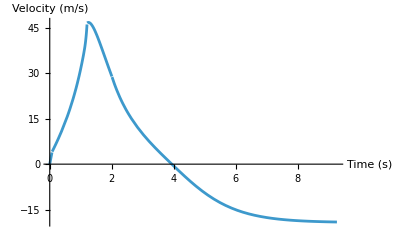

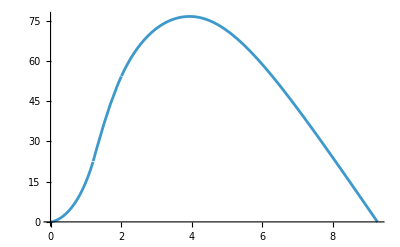

```mathematica
Plot[yrocket'[t],{t,0,maxtimeall}, AxesLabel->{"Time (s)", "Velocity (m/s)"}]
Plot[yrocket[t], {t, 0, maxtimeall}]
```

```mathematica
FindMaximum[yrocket[t],{t,0,maxtimeall}]
```

{76.6207,{t→3.94078}}